# Critical exponents: K=1.

## Felipe Ortega , May 2018

## Gap data C1: Param, C2: Ground energy, C3: Gap, C4: Sec der, C5; order C6: binder, C7: susc Careful: csvs with order parameters have gap/puncture instead of just gap!

```mathematica
ClearAll[pun6,pun7,pun8,pun9,pun10]
dir="Dropbox/Essay/Codes/Torus/binderandsusc";
pun6=Import["results/csvfiles/Np_6_2018-05-18.csv",Path->dir,"HeaderLines"->1];
pun7=Import["results/csvfiles/Np_7_2018-05-18.csv",Path->dir,"HeaderLines"->1];
pun8=Import["results/csvfiles/Np_8_2018-05-18.csv",Path->dir,"HeaderLines"->1];
pun9=Import["results/csvfiles/Np_9_2018-05-18.csv",Path->dir,"HeaderLines"->1];
pun10=Import["results/csvfiles/Np_10_2018-05-18.csv",Path->dir,"HeaderLines"->1];
```

## Finite size analysis

```mathematica
xaxis[lam_,L_,ν_,lamc_]:=L^(1/ν)(lam-lamc);
```

### Binder cummulant ν =0.221(1), λ_c = 0.6966 (numerical for ν and λ_c)

#### Interactive procedure and manual (Add times the puncture to make it gap)

```mathematica
Manipulate[
gg6=Table[{xaxis[pun6[[i,1]],Sqrt[6],ν,λ],pun6[[i,6]]},{i,Length[pun6]}];
gg7=Table[{xaxis[pun7[[i,1]],Sqrt[7],ν,λ],pun7[[i,6]]},{i,Length[pun7]}];gg8=Table[{xaxis[pun8[[i,1]],Sqrt[8],ν,λ],pun8[[i,6]]},{i,Length[pun8]}];
gg9=Table[{xaxis[pun9[[i,1]],Sqrt[9],ν,λ],pun9[[i,6]]},{i,Length[pun9]}];gg10=Table[{xaxis[pun10[[i,1]],Sqrt[10],ν,λ],pun10[[i,6]]},{i,Length[pun10]}];
ListPlot[{
gg6,
gg7,
gg8,
gg9,
gg10},
(*Joined->True,*)(*Mesh->Full,*)
PlotRange->All(*{{-0.01,0.01},{1,1.5}}*),
PlotLegends->Automatic],
{{ν,0.221},0.01,1},
{{λ,0.6966},0.6,.8}]
```

#### Latex plot

```mathematica
Needs["MaTeX`"]
fontSize=11;
SetOptions[MaTeX,FontSize->fontSize];
SetOptions[Plot,BaseStyle->{FontSize->fontSize,FontFamily->"CMU Serif"}];
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

BlackFrame::shdw: Symbol BlackFrame appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

Markers:

```mathematica
tr=Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}];
sq=Polygon[{{1,0},{1,1},{0,1},{0,0}}];
cr=Line[{{0,0},{0,2},{0,1},{1,1},{-1,1}}];
```

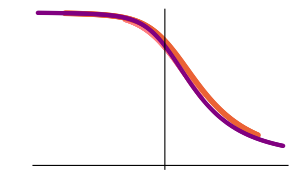

```mathematica
gg6=Table[{xaxis[pun6[[i,1]],Sqrt[6],ν,λ],pun6[[i,6]]},{i,Length[pun6]}]/.{ν->0.221,λ->0.6966};
gg7=Table[{xaxis[pun7[[i,1]],Sqrt[7],ν,λ],pun7[[i,6]]},{i,Length[pun7]}]/.{ν->0.221,λ->0.6966};gg8=Table[{xaxis[pun8[[i,1]],Sqrt[8],ν,λ],pun8[[i,6]]},{i,Length[pun8]}]/.{ν->0.221,λ->0.6966};
gg9=Table[{xaxis[pun9[[i,1]],Sqrt[9],ν,λ],pun9[[i,6]]},{i,Length[pun9]}]/.{ν->0.221,λ->0.6966};gg10=Table[{xaxis[pun10[[i,1]],Sqrt[10],ν,λ],pun10[[i,6]]},{i,Length[pun10]}]/.{ν->0.221,λ->0.6966};
ffbind=ListPlot[{
gg6,
gg7,
gg8,
gg9,
gg10},
PlotRange->{0.65,1}(*{{-0.01,0.01},{1,1.5}}*),
PlotLegends->Placed[
PointLegend[
{Pink,Orange,Green,Cyan,Purple},
Table[MaTeX[ii],{ii,6,10}],
 LegendLabel->MaTeX[HoldForm[Subscript[N, F]]]],
{Scaled[{0.2,0.01}],Scaled[{1,0}]}],
PlotMarkers->{
Graphics[{Pink,Thickness[0.05],Circle[]},ImageSize->3],
Graphics[{EdgeForm[Directive[Thickness[0.05],Orange]],Transparent,tr},ImageSize->3],
Graphics[{EdgeForm[Directive[Thickness[0.05],Green]],Transparent,sq},ImageSize->3],
Graphics[{Thickness[0.05],Cyan,cr},ImageSize->3],
Graphics[{Purple,Thickness[0.05],Circle[]},ImageSize->3]}];
figbind=Show[ffbind,
Ticks->{Table[{x,MaTeX[x,"DisplayStyle"->False]},{x,-6,6,3}],
Table[{x,MaTeX[x,"DisplayStyle"->False]},{x,0.6,1, 0.1}]},
AxesStyle->BlackFrame,
AxesLabel->MaTeX[{HoldForm[(λ-0.697)],HoldForm[Ũ]}],
ImageSize->300 ]
```

```mathematica
Export["~/Dropbox/Essay/Essay/Actualessay/F_Ortega_Figs/bindercum.pdf",figbind]
```

~/Dropbox/Essay/Essay/Actualessay/F_Ortega_Figs/bindercum.pdf

Quantitative procedure
Find the minimal distance between curves

#### Quantitative estimation of ν

Try to fix xmin and xmax to be symmetric around x=0.

```mathematica
νmin=0.19;
νmax=0.23;
νstep=0.01;
lammin=0.695;
lammax=0.70;
lamstep=0.001;
gaptab={pun6,pun7,pun8,pun9,pun10};
Ltab={6,7,8,9,10};
NSpec=Length[Ltab];
ClearAll[integral];
Do[
Do[
gapintrp = Table[
Interpolation[Table[{xaxis[gaptab[[j]][[i,1]],Sqrt[Ltab[[j]]],ν,lambdacg],gaptab[[j]][[i,6]]},{i,Length[pun7]}]],{j,NSpec}];
xmin=xaxis[gaptab[[1]][[1,1]],Sqrt[Ltab[[1]]],ν,lambdacg];
xmax=xaxis[gaptab[[1]][[226,1]],Sqrt[Ltab[[1]]],ν,lambdacg];
Print[ν];
integral[ν,lambdacg]=1/(xmax-xmin)NIntegrate[1/NSpec Sum[(gapintrp[[j]][x])^2,{j,1,NSpec}]-(1/NSpec Sum[gapintrp[[j]][x],{j,1,NSpec}])^2,
{x,xmin,xmax}],
{ν,νmin,νmax,νstep}];
Print[Table[{ν,integral[ν,lambdacg]},{ν,νmin,νmax,νstep}]],
{lambdacg,lammin,lammax,lamstep}];
```

0.19

0.2

0.21

0.22

0.23

{{0.19,0.0000810302},{0.2,0.0000717419},{0.21,0.0000651976},{0.22,0.0000610409},{0.23,0.0000589404}}

0.19

0.2

0.21

0.22

0.23

{{0.19,0.0000673464},{0.2,0.0000608972},{0.21,0.0000569772},{0.22,0.0000552207},{0.23,0.0000552965}}

0.19

0.2

0.21

0.22

0.23

{{0.19,0.0000605202},{0.2,0.0000564104},{0.21,0.0000546473},{0.22,0.0000548561},{0.23,0.0000567062}}

0.19

0.2

0.21

0.22

0.23

{{0.19,0.0000609851},{0.2,0.0000586313},{0.21,0.0000584895},{0.22,0.0000601743},{0.23,0.0000633528}}

0.19

0.2

0.21

0.22

0.23

{{0.19,0.000069126},{0.2,0.0000678697},{0.21,0.0000687533},{0.22,0.000071376},{0.23,0.0000753979}}

0.19

0.2

0.21

0.22

0.23

{{0.19,0.0000852766},{0.2,0.0000843949},{0.21,0.0000856553},{0.22,0.0000886356},{0.23,0.0000929821}}

```mathematica
ListPlot3D[Flatten[Table[{lambdacg,ν,integral[ν,lambdacg]},{ν,νmin,νmax,νstep},{lambdacg,lammin,lammax,lamstep}],1],Mesh->All]
data=Flatten[Table[{lambdacg,ν,integral[ν,lambdacg]},{ν,νmin,νmax,νstep},{lambdacg,lammin,lammax,lamstep}],1];
fun[x_,y_]:=Normal@NonlinearModelFit[data,a x^2+b x +c+d y^2+e y +f x y,{a,b,c,d,e,f},{x,y}];
FindMinimum[fun[x,y],{x,y}]
```

-Graphics3D-

{0.0000535178,{x→0.696622,y→0.221012}}

### Gap related calculation yields z = 3.55 ν =0.221(1), λ_c = 0.6966(5) (numerical fro z and λ_c)

#### Interactive procedure and manual (Add times the puncture to make it gap)

```mathematica
Manipulate[
gg6=Table[{xaxis[pun6[[i,1]],Sqrt[6],ν,λ],Sqrt[6]^z  6*pun6[[i,3]]},{i,Length[pun6]}];
gg7=Table[{xaxis[pun7[[i,1]],Sqrt[7],ν,λ],Sqrt[7]^z  7*pun7[[i,3]]},{i,Length[pun7]}];gg8=Table[{xaxis[pun8[[i,1]],Sqrt[8],ν,λ],Sqrt[8]^z  8*pun8[[i,3]]},{i,Length[pun8]}];
gg9=Table[{xaxis[pun9[[i,1]],Sqrt[9],ν,λ],Sqrt[9]^z  9*pun9[[i,3]]},{i,Length[pun9]}];gg10=Table[{xaxis[pun10[[i,1]],Sqrt[10],ν,λ],Sqrt[10]^z  10*pun10[[i,3]]},{i,Length[pun10]}];
ListPlot[{
gg6,
gg7,
gg8,
gg9,
gg10},
Joined->True,(*Mesh->Full,*)
PlotRange->All(*{{-0.01,0.01},{1,1.5}}*),
PlotLegends->Automatic],
{{z,3.55},-10,20},
{{ν,0.221},0,2},
{{λ,0.6966},0.6,.8}]
```

Quantitative procedure
Find the minimal distance between curves  (Add times the puncture to make it gap)

#### Latex plots

```mathematica
ScientificForm[0.004]//TeXForm
```

4.\times 10^{-3}

```mathematica
Needs["MaTeX`"]
fontSize=9;
SetOptions[MaTeX,FontSize->fontSize];
SetOptions[Plot,BaseStyle->{FontSize->fontSize,FontFamily->"CMU Serif"}];
```

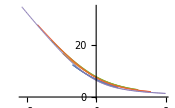

```mathematica
gg6=Table[{xaxis[pun6[[i,1]],Sqrt[6],ν,λ],Sqrt[6]^z  6*pun6[[i,3]]},{i,Length[pun6]}]/.{z->3.55,ν->0.221,λ->0.6966};
gg7=Table[{xaxis[pun7[[i,1]],Sqrt[7],ν,λ],Sqrt[7]^z  7*pun7[[i,3]]},{i,Length[pun7]}]/.{z->3.55,ν->0.221,λ->0.6966};gg8=Table[{xaxis[pun8[[i,1]],Sqrt[8],ν,λ],Sqrt[8]^z  8*pun8[[i,3]]},{i,Length[pun8]}]/.{z->3.55,ν->0.221,λ->0.6966};
gg9=Table[{xaxis[pun9[[i,1]],Sqrt[9],ν,λ],Sqrt[9]^z  9*pun9[[i,3]]},{i,Length[pun9]}]/.{z->3.55,ν->0.221,λ->0.6966};gg10=Table[{xaxis[pun10[[i,1]],Sqrt[10],ν,λ],Sqrt[10]^z  10*pun10[[i,3]]},{i,Length[pun10]}]/.{z->3.55,ν->0.221,λ->0.6966};
collaps2=ListPlot[{
gg6,
gg7,
gg8,
gg9,
gg10},
(*Mesh->Full,*)
PlotRange->All(*{{-0.01,0.01},{1,1.5}}*),
PlotLegends->Table[ii,{ii,6,10}],
ImageSize->175]
```

```mathematica
Export["~/Dropbox/Essay/Essay/Actualessay/F_Ortega_Figs/collapse2.pdf",collaps2]
```

~/Dropbox/Essay/Essay/Actualessay/F_Ortega_Figs/collapse2.pdf

#### Quantitative estimation of ν

```mathematica
gaptab[[1]][[38-20,1]]-gaptab[[1]][[38,1]]
```

-0.008

Try to fix xmin and xmax to be symmetric around x=0.

```mathematica
bestν=0.221;
bestlam=0.697;
zmin=3.4;
zmax=3.8;
zstep=0.05;
ClearAll[crosspos,var,integral,gapintrp]
Ltab = {6,7,8,9,10};
gaptab = {pun6,pun7,pun8,pun9,pun10};
NSpec=Length[Ltab];
Do[
gapintrp = Table[
Interpolation[Table[{xaxis[gaptab[[j]][[i,1]],Sqrt[Ltab[[j]]],bestν,bestlam],Sqrt[Ltab[[j]]]^z Ltab[[j]]gaptab[[j]][[i,3]]},{i,Length[pun7]}]],{j,NSpec}];
xmin=xaxis[gaptab[[1]][[1,1]],Sqrt[Ltab[[1]]],bestν,bestlam];
xmax=xaxis[gaptab[[1]][[226,1]],Sqrt[Ltab[[1]]],bestν,bestlam];
integralnum[z]=1/(xmax-xmin)NIntegrate[1/NSpec Sum[(gapintrp[[j]][x])^2,{j,1,NSpec}]-(1/NSpec Sum[gapintrp[[j]][x],{j,1,NSpec}])^2,
{x,xmin,xmax}];
integralden[z]=1/(xmax-xmin)NIntegrate[(1/NSpec Sum[gapintrp[[j]][x],{j,1,NSpec}])^2,{x,xmin,xmax}];
Print[z],
{z,zmin,zmax,zstep}];
```

3.4

3.45

3.5

3.55

3.6

3.65

3.7

3.75

3.8

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

3.55003

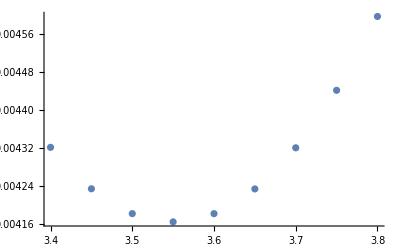

```mathematica
Subscript[ℛ, 2]=Line[{{zmin,0},{zmax,0}}];
data=Table[{z,integralnum[z]/integralden[z]},{z,zmin,zmax,zstep}];
bestz =x/.NMinimize[Interpolation[Table[{z,integralnum[z]/integralden[z]},{z,zmin,zmax,zstep}]][x],{x,r}∈Subscript[ℛ, 2]][[2]]
Show[ListPlot[data,PlotRange->All]]
```

### Specific Heat α =1.08 (y = -4.93), ν= 0.221(0.01), λ_c =0.6966(1)

#### Interactive procedure (and y estimation) (Add times -λ)

```mathematica
Manipulate[
ss6=Table[{xaxis[pun6[[i,1]],Sqrt[6],ν,λ],-pun6[[i,1]] Sqrt[6]^y  pun6[[i,4]]},{i,2,Length[pun6]-1}];
ss7=Table[{xaxis[pun7[[i,1]],Sqrt[7],ν,λ],-pun7[[i,1]] Sqrt[7]^y  pun7[[i,4]]},{i,2,Length[pun7]-1}];ss8=Table[{xaxis[pun8[[i,1]],Sqrt[8],ν,λ],-pun8[[i,1]] Sqrt[8]^y  pun8[[i,4]]},{i,2,Length[pun8]-1}];
ss9=Table[{xaxis[pun9[[i,1]],Sqrt[9],ν,λ],-pun9[[i,1]] Sqrt[9]^y  pun9[[i,4]]},{i,2,Length[pun9]-1}];ss10=Table[{xaxis[pun10[[i,1]],Sqrt[10],ν,λ],-pun10[[i,1]] Sqrt[10]^y  pun10[[i,4]]},{i,2,Length[pun10]-1}];
ListPlot[{
ss6,
ss7,
ss8,
ss9,
ss10},
Joined->True,(*Mesh->Full,*)
PlotRange->All(*{{0.5,0.7},{0,20*Min[9^z pun9]}}*),
PlotLegends->Automatic],
{{y,-3.361},-10,10},
{{ν,0.221},0.01,.24},
{{λ,0.6966},0.6,.8}]
```

#### Quantitative ν

```mathematica
bestν=0.221;
bestlam=0.697;
ymin=-5.2;
ymax=-4.8;
ystep=0.1;
ClearAll[crosspos,var,integral1,integral2,secintrp]
Ltab = {6,7,8,9,10};
sectab = {pun6,pun7,pun8,pun9,pun10}; 
NSpec=Length[Ltab];
Do[
secintrp = Table[
Interpolation[Table[{xaxis[sectab[[j]][[i,1]],Sqrt[Ltab[[j]]],bestν,bestlam],-sectab[[j]][[i,1]] Sqrt[Ltab[[j]]]^y sectab[[j]][[i,4]]},{i,Length[pun7]}]],{j,NSpec}];
xmin=xaxis[sectab[[1]][[3,1]],Sqrt[Ltab[[1]]],bestν,bestlam];
xmax=xaxis[sectab[[1]][[224,1]],Sqrt[Ltab[[1]]],bestν,bestlam];
integral1[y]=1/(xmax-xmin)NIntegrate[1/NSpec Sum[(secintrp[[j]][x])^2,{j,1,NSpec}],{x,xmin,xmax}];
integral2[y]=1/(xmax-xmin)NIntegrate[(1/NSpec Sum[secintrp[[j]][x],{j,1,NSpec}])^2,{x,xmin,xmax}];
Print[y],
{y,ymin,ymax,ystep}];
```

-5.2

-5.1

-5.

-4.9

-4.8

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-4.93087

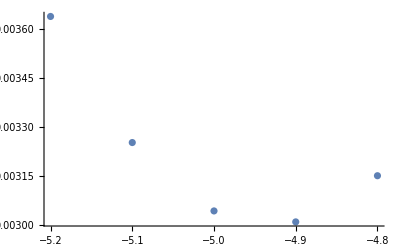

```mathematica
Subscript[ℛ, 2]=Line[{{ymin,0},{ymax,0}}];
data=Table[{y,integral1[y]/integral2[y]-1},{y,ymin,ymax,ystep}];
bestz =x/.NMinimize[Interpolation[Table[{y,integral1[y]/integral2[y]-1},{y,ymin,ymax,ystep}]][x],{x,r}∈Subscript[ℛ, 2]][[2]]
Show[ListPlot[data,PlotRange->All]]
```

### Order parameter β =0.015 (w = 0.07 (.1)), ν= 0.221(1), λ_c = 0.6966

```mathematica
Manipulate[
ord6=Table[{xaxis[pun6[[i,1]],Sqrt[6],ν,λ],Sqrt[6]^w  pun6[[i,5]]},{i,Length[pun6]}];
ord7=Table[{xaxis[pun7[[i,1]],Sqrt[7],ν,λ],Sqrt[7]^w  pun7[[i,5]]},{i,Length[pun7]}];ord8=Table[{xaxis[pun8[[i,1]],Sqrt[8],ν,λ],Sqrt[8]^w  pun8[[i,5]]},{i,Length[pun8]}];
ord9=Table[{xaxis[pun9[[i,1]],Sqrt[9],ν,λ],Sqrt[9]^w  pun9[[i,5]]},{i,Length[pun9]}];ord10=Table[{xaxis[pun10[[i,1]],Sqrt[10],ν,λ],Sqrt[10]^w  pun10[[i,5]]},{i,Length[pun10]}];
ListPlot[{
ord6,
ord7,
ord8,
ord9,
ord10},
Joined->True,(*Mesh->Full,*)
PlotRange->All(*{{-0.01,0.01},{1,1.5}}*),
PlotLegends->Automatic],
{{w,0.935},-1,2},
{{ν,0.221},-1,1},
{{λ,0.6966},0.6,.8}]
```

#### Qualitative exponent

```mathematica
bestν=0.221;
bestlam=0.697;
wmin=-0.5;
wmax=0.5;
wstep=0.2;
ClearAll[crosspos,var,ordintrp]
Ltab = {6,7,8,9,10};
ordtab = {pun6,pun7,pun8,pun9,pun10};
NSpec=Length[Ltab];
Do[
ordintrp = Table[
Interpolation[Table[{xaxis[ordtab[[j]][[i,1]],Sqrt[Ltab[[j]]],bestν,bestlam],Sqrt[Ltab[[j]]]^w ordtab[[j]][[i,5]]},{i,Length[pun7]}]],{j,NSpec}];
xmin=xaxis[sectab[[1]][[1,1]],Sqrt[Ltab[[1]]],bestν,bestlam];
xmax=xaxis[sectab[[1]][[226,1]],Sqrt[Ltab[[1]]],bestν,bestlam];
integral1[w]=1/(xmax-xmin)NIntegrate[1/NSpec Sum[(ordintrp[[j]][x])^2,{j,1,NSpec}],{x,xmin,xmax}];
integral2[w]=1/(xmax-xmin)NIntegrate[(1/NSpec Sum[ordintrp[[j]][x],{j,1,NSpec}])^2,{x,xmin,xmax}];
Print[w],
{w,wmin,wmax,wstep}];
```

-0.5

-0.3

-0.1

0.1

0.3

0.5

0.0670284

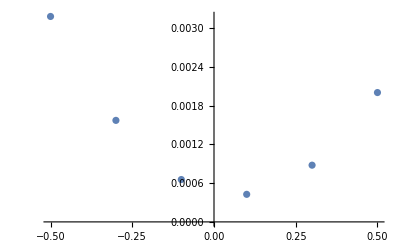

```mathematica
Subscript[ℛ, 2]=Line[{{wmin,0},{wmax,0}}];
data=Table[{y,integral1[y]/integral2[y]-1},{y,wmin,wmax,wstep}];
bestz =x/.NMinimize[Interpolation[Table[{y,integral1[y]/integral2[y]-1},{y,wmin,wmax,wstep}]][x],{x,r}∈Subscript[ℛ, 2]][[2]]
Show[ListPlot[data,PlotRange->All]]
```

### Susceptibility γ = 0.0442 (v = -2.08 (.1)), ν= 0.221(1), λ_c = 0.6966

```mathematica
Manipulate[
ord6=Table[{xaxis[pun6[[i,1]],Sqrt[6],ν,λ],Sqrt[6]^v  pun6[[i,7]]},{i,Length[pun6]}];
ord7=Table[{xaxis[pun7[[i,1]],Sqrt[7],ν,λ],Sqrt[7]^v  pun7[[i,7]]},{i,Length[pun7]}];ord8=Table[{xaxis[pun8[[i,1]],Sqrt[8],ν,λ],Sqrt[8]^v  pun8[[i,7]]},{i,Length[pun8]}];
ord9=Table[{xaxis[pun9[[i,1]],Sqrt[9],ν,λ],Sqrt[9]^v  pun9[[i,7]]},{i,Length[pun9]}];ord10=Table[{xaxis[pun10[[i,1]],Sqrt[10],ν,λ],Sqrt[10]^v  pun10[[i,7]]},{i,Length[pun10]}];
ListPlot[{
ord6,
ord7,
ord8,
ord9,
ord10},
Joined->True,(*Mesh->Full,*)
PlotRange->All(*{{-0.01,0.01},{1,1.5}}*),
PlotLegends->Automatic],
{{v,-2.08},-3,2},
{{ν,0.221},-1,1},
{{λ,0.6966},0.6,.8}]
```

```mathematica
wmin=0.5;
wmax=1.5;
wstep=0.01;
ClearAll[crosspos,var,ordintrp]
Do[
Ltab = {6,7,8,9,10};
ordtab = {pun6,pun7,pun8,pun9,pun10};
NSpec=Length[Ltab];
ordintrp = Table[
Interpolation[Table[{ordtab[[j]][[i,1]],Sqrt[Ltab[[j]]]^w ordtab[[j]][[i,5]]},{i,Length[pun7]}]],{j,NSpec}];
crosspos=Table[
(x/.FindRoot[ ordintrp[[aa]][x]==ordintrp[[bb]][x],{x,0.675,.66,.72}]),{aa,1,NSpec},{bb,aa+1,NSpec}];
var[w] =Flatten[crosspos];
Print[w],
{w,wmin,wmax,wstep}]
```

0.5

0.51

0.52

0.53

0.54

0.55

0.56

0.57

0.58

0.59

0.6

0.61

0.62

0.63

0.64

0.65

0.66

0.67

0.68

0.69

0.7

0.71

0.72

0.73

0.74

0.75

0.76

0.77

0.78

0.79

0.8

0.81

0.82

0.83

0.84

0.85

0.86

0.87

0.88

0.89

0.9

0.91

0.92

0.93

0.94

0.95

0.96

0.97

0.98

0.99

1.

1.01

1.02

1.03

1.04

1.05

1.06

1.07

1.08

1.09

1.1

1.11

1.12

1.13

1.14

1.15

1.16

1.17

1.18

1.19

1.2

1.21

1.22

1.23

1.24

1.25

1.26

1.27

1.28

1.29

1.3

1.31

1.32

1.33

1.34

1.35

1.36

1.37

1.38

1.39

1.4

1.41

1.42

1.43

1.44

1.45

1.46

1.47

1.48

1.49

1.5

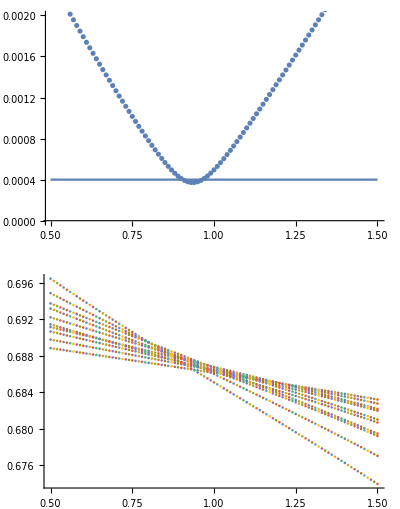

0.93465

0.687067

```mathematica
ClearAll[varval,sdevval,meanval]
Subscript[ℛ, 2]=Line[{{wmin,0},{wmax,0}}];
lps=ListPlot[Table[{i,var[i][[a]]},{i,wmin,wmax,wstep},{a,NSpec(NSpec-1)/2}],PlotRange->All];
Do[varval[i]=Variance[var[i]];
sdevval[i]=StandardDeviation[var[i]];
meanval[i] = Mean[var[i]],
{i,wmin,wmax,wstep}]
vaps =ListPlot[Table[{i,sdevval[i]},{i,wmin,wmax,wstep}],PlotRange->{0,0.002}];
GraphicsColumn[{Show[vaps,Plot[0.09/225,{w,wmin,wmax}]],lps}]
bestw =x/.NMinimize[Interpolation[Table[{i,varval[i]},{i,wmin,wmax,wstep}]][x],{x,y}∈Subscript[ℛ, 2]][[2]]
lamdaco=Interpolation[Table[{i,meanval[i]},{i,wmin,wmax,wstep}]][wbest]
```

```mathematica
gaptab[[1]][[94,1]]
gaptab[[1]][[94-20,1]]-gaptab[[1]][[94,1]]
```

0.6872

-0.008

```mathematica
νmin=0.15;
νmax=0.2;
νstep=0.005;
ClearAll[bestν]
Do[
Do[
ordintrp = Table[
Interpolation[Table[{xaxis[ordtab[[j]][[i,1]],Sqrt[Ltab[[j]]],ν,lamdaco],Sqrt[Ltab[[j]]]^bestw ordtab[[j]][[i,5]]},{i,Length[pun7]}]],{j,NSpec}];
xmin=xaxis[ordtab[[1]][[94-dist,1]],Sqrt[Ltab[[1]]],ν,lamdaco];
xmax=xaxis[ordtab[[1]][[94+dist,1]],Sqrt[Ltab[[1]]],ν,lamdaco];
integral[ν]=1/(xmax-xmin)NIntegrate[1/NSpec Sum[(ordintrp[[j]][x])^2,{j,1,NSpec}]-(1/NSpec Sum[ordintrp[[j]][x],{j,1,NSpec}])^2,
{x,xmin,xmax}],
{ν,νmin,νmax,νstep}];
Subscript[ℛ, 3]=Line[{{νmin,0},{νmax,0}}];
bestν[dist]=x/.NMinimize[Interpolation[Table[{ν,integral[ν]},{ν,νmin,νmax,νstep}]][x],{x,y}∈Subscript[ℛ, 3]][[2]];
Print[dist],
{dist,{10,12,14,16,18,20}}];
```

10

12

14

16

18

20

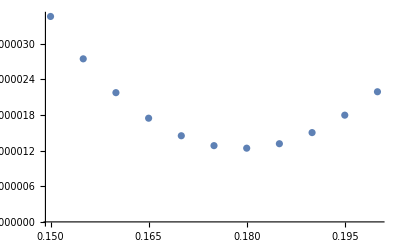

```mathematica
ListPlot[Table[{ν,integral[ν]},{ν,νmin,νmax,νstep}],PlotRange->All]
```

0.179381

0.0000616972

0.179077+0.0000591889 x-2.46608×10^-6 x^2

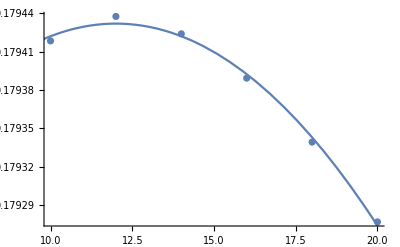

```mathematica
data=Table[{dist,bestν[dist]},{dist,{10,12,14,16,18,20}}];
data2 =Table[bestν[dist],{dist,{10,12,14,16,18,20}}];
Mean[data2]
StandardDeviation[data2]
parab=Normal@NonlinearModelFit[data,a x^2+b x +c,{a,b,c},x]
Show[ListPlot[data,PlotRange->All],Plot[parab,{x,0,20}]]
```

## Hyper-scaling relation 2-α =ν(d+z) (α = -y·ν) It kinda imporves...

Only gap values

```mathematica
.21(2+3.43+4.93-.15)
```

2.1441

```mathematica
2-1.116-0.221(2+3.5)
zeta=3.5;
νu=0.221;
alp=2-νu(2+zeta)
y=-alp/νu
```

-0.3315

0.7845

-3.54977

Eta from specific heat/order

```mathematica
zeta=0.259;
νu=0.113;
alp=2-νu(2+zeta)
eta=-alp/νu
```

1.74473

-15.4401

Supposing is a one - dimensional model

```mathematica
zeta=1.64/2;
νu=0.237*2;
alp=2-νu(1+zeta)
eta=-alp/νu
eta2d=eta*2
```

1.13732

-2.39941

-4.79882

```mathematica
d
```